```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/Ratesfunc.nb"}]];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
Rstar =RSS;
Hstar =HSS;
Fstar = FSS;
StarRates={Rstar,Hstar,Fstar}/.{λ->ConsumerGrowth,μ->Mortality,β->FullMaintenance,δ->StarveMaintenance,α->ResourceGrowth,σ->Starvation,ρ->Recovery};
dimR = dimRSS[StarRates[[1]]];
dimH = dimSS[StarRates[[2]]];
dimF = dimSS[StarRates[[3]]];
```

Energy equivalence hypothesis

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv"}],"csv"];
```

```mathematica
Mean[data[[All,2]]]
```

0.000791639

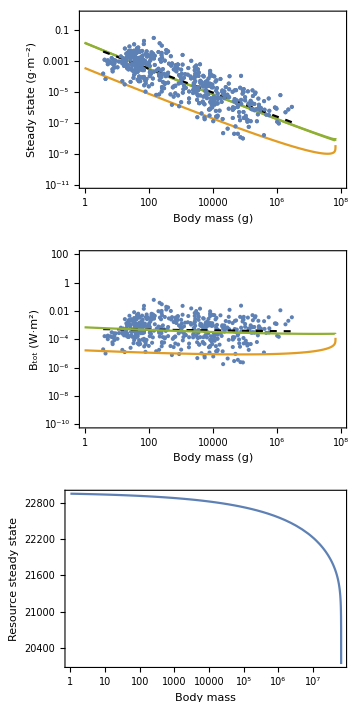

```mathematica
Cplot=GraphicsGrid[{{
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (g·m^-2)"}],
LogLogPlot[{dimH/M,dimF/M},{M,1,10^8},PlotStyle->{ColorData[97,2],ColorData[97,3]}],
LogLogPlot[(dimH/M)+(dimF/M),{M,1,10^8},PlotStyle->ColorData[97,3]]
,LogLogPlot[0.0115643*M^(-0.776818),{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],
ListLogLogPlot[data]
}]
},{
Show[{
ListLogLogPlot[Table[{data[[i]][[1]],data[[i]][[2]]*(data[[i]][[1]])^(3/4)*B0},{i,Length[data]}],PlotRange->{{1,10^8},{10^-10,100}},Frame->True,FrameLabel->{"Body mass (g)","B_tot (W·m^2)"}],
LogLogPlot[0.0115643*M^(-0.776818)*M^(3/4)*B0,{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],
LogLogPlot[{dimH/M*M^(3/4)*B0,dimF/M*M^(3/4)*B0},{M,1,10^8},Frame->True,FrameLabel->{"Body mass (g)","B_tot"},PlotStyle->{ColorData[97,2],ColorData[97,3]}]}]
},{
LogLinearPlot[dimR,{M,1,10^8},Frame->True,PlotRange->All,FrameLabel->{"Body mass","Resource steady state"}]
}}]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_FPAllometric.pdf"}],Cplot,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_FPAllometric.pdf

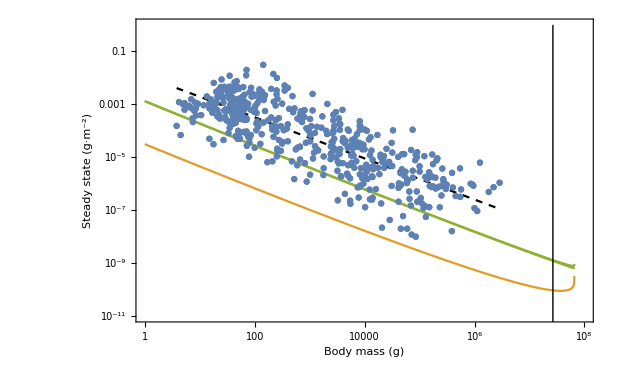

```mathematica
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (g·m^-2)"}],
LogLogPlot[{dimH/M,dimF/M},{M,1,10^8},PlotStyle->{ColorData[97,2],ColorData[97,3]}],
LogLogPlot[(dimH/M)+(dimF/M),{M,1,10^8},PlotStyle->ColorData[97,3]]
,LogLogPlot[0.0115643*M^(-0.776818),{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],
ListLogLogPlot[data],
Graphics[Line[{{Log@(2.66312453830273*^7),Log@(10^-15)},{Log@(2.66312453830273*^7),Log@(1)}}]]
}]
```

```mathematica
NSolve[(dimH/M)+(dimF/M)==Infinity,M]
```

NSolve::infc: The system (2.70754×10^-8 (-(1.41054×10^-6)/(M^(1/4) Log[Times[«2»]])+(«22»)/(M^(«1») «1»)) (-0.0152263/(M^(1/4) Log[Times[«2»]])+4535/(Times[«3»]+Times[«3»])))/(√M Log[(«21»)/Plus[«2»]] («1») «1» ((«22»)/(«1»)-(«21»)/(«1»)) (-(0.0304493 (Times[«4»]+Times[«5»]))/(M^(1/4) Log[«1»] Plus[«2»])+(2.3677×10^-12 («1»))/(√M Log[«1»] Log[«1»])))-(«1»)/(«1»)==∞ contains an infinite object ∞.

NSolve[(2.70754×10^-8 (-(1.41054×10^-6)/(M^(1/4) Log[0.0127415/(1-0.0176465/M^0.02)])+(6.71429×10^-6)/(M^(1/4) Log[1-0.0202 M^0.19])) (-0.0152263/(M^(1/4) Log[0.0127415/(1-0.987259 (1-0.0202 M^0.19)^(1/4))])+4535/(148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M])))/(√M Log[0.0127415/(1-0.0176465/M^0.02)] (2.63558×10^-8 (1/(1-0.0176465/M^0.02))^4. (-2.90908×10^-7 M^0.92+(-(2.32051×10^7 (-1+0.0176465/M^0.02))/((1/(1-0.0176465/M^0.02))^3.)-(221750. (-1+0.0176465/M^0.02)^2)/((1/(1-0.0176465/M^0.02))^2.)-(1255.74 (-1+0.0176465/M^0.02)^3)/((1/(1-0.0176465/M^0.02))^1.)+3 (-1+0.0000219804/M^0.06-0.00186839/M^0.04+0.070586/M^0.02)) M-(4.55308×10^8 M Log[0.0127415/(1-0.0176465/M^0.02)])/((1/(1-0.0176465/M^0.02))^4.))+((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^4. (2.90908×10^-7 M^0.92+(3 (1-0.0000219804/M^0.06+0.00186839/M^0.04-0.070586/M^0.02)+(48 (-1+0.0176465/M^0.02))/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^3.)+(36 (-1+0.0176465/M^0.02)^2)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^2.)+(16 (-1+0.0176465/M^0.02)^3)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^1.)) M+(12. M Log[(1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02)])/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^4.))) (148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M])^2 ((2.14774×10^-8)/(√M Log[0.0127415/(1-0.987259 (1-0.0202 M^0.19)^(1/4))] Log[0.0127415/(1-0.0176465/M^0.02)])-0.0304493/(M^(1/4) Log[1-0.0202 M^0.19] (148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M]))) (-((0.0304493 (-1/(M^(1/4) Log[0.0127415/(1-0.0176465/M^0.02)])1.41054×10^-6 (-(1.67857×10^-6)/(M^(1/4) Log[0.0127415/(1-0.987259 (1-0.0202 M^0.19)^(1/4))])+(5.73802×10^-7 √M)/(2.63558×10^-8 (1/(1-0.0176465/M^0.02))^4. (-2.90908×10^-7 M^0.92+(-(2.32051×10^7 (-1+0.0176465/M^0.02))/((1/(1-0.0176465/M^0.02))^3.)-(221750. (-1+0.0176465/M^0.02)^2)/((1/(1-0.0176465/M^0.02))^2.)-(1255.74 (-1+0.0176465/M^0.02)^3)/((1/(1-0.0176465/M^0.02))^1.)+3 (-1+0.0000219804/M^0.06-0.00186839/M^0.04+0.070586/M^0.02)) M-(4.55308×10^8 M Log[0.0127415/(1-0.0176465/M^0.02)])/((1/(1-0.0176465/M^0.02))^4.))+((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^4. (2.90908×10^-7 M^0.92+(3 (1-0.0000219804/M^0.06+0.00186839/M^0.04-0.070586/M^0.02)+(48 (-1+0.0176465/M^0.02))/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^3.)+(36 (-1+0.0176465/M^0.02)^2)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^2.)+(16 (-1+0.0176465/M^0.02)^3)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^1.)) M+(12. M Log[(1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02)])/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^4.))))+(0.222196 M^(3/4) ((2.58242×10^-6)/M^(1/4)-1/(M Log[0.0127415/(1-0.0176465/M^0.02)])8.36467×10^-14 (1/(1-0.0176465/M^0.02))^4. (2.90908×10^-7 (-1+(3.79423×10^7)/((1/(1-0.0176465/M^0.02))^4.)) M^0.92+(-(2.32051×10^7 (-1+0.0176465/M^0.02))/((1/(1-0.0176465/M^0.02))^3.)-(221750. (-1+0.0176465/M^0.02)^2)/((1/(1-0.0176465/M^0.02))^2.)-(1255.74 (-1+0.0176465/M^0.02)^3)/((1/(1-0.0176465/M^0.02))^1.)+3 (-1+0.0000219804/M^0.06-0.00186839/M^0.04+0.070586/M^0.02)+(3.79423×10^7 (-25+0.0000219804/M^0.06+0.00186839/M^0.04+0.211758/M^0.02))/((1/(1-0.0176465/M^0.02))^4.)) M-(4.55308×10^8 M Log[0.0127415/(1-0.0176465/M^0.02)])/((1/(1-0.0176465/M^0.02))^4.))))/((2.63558×10^-8 (1/(1-0.0176465/M^0.02))^4. (-2.90908×10^-7 M^0.92+(-(2.32051×10^7 (-1+0.0176465/M^0.02))/((1/(1-0.0176465/M^0.02))^3.)-(221750. (-1+0.0176465/M^0.02)^2)/((1/(1-0.0176465/M^0.02))^2.)-(1255.74 (-1+0.0176465/M^0.02)^3)/((1/(1-0.0176465/M^0.02))^1.)+3 (-1+0.0000219804/M^0.06-0.00186839/M^0.04+0.070586/M^0.02)) M-(4.55308×10^8 M Log[0.0127415/(1-0.0176465/M^0.02)])/((1/(1-0.0176465/M^0.02))^4.))+((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^4. (2.90908×10^-7 M^0.92+(3 (1-0.0000219804/M^0.06+0.00186839/M^0.04-0.070586/M^0.02)+(48 (-1+0.0176465/M^0.02))/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^3.)+(36 (-1+0.0176465/M^0.02)^2)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^2.)+(16 (-1+0.0176465/M^0.02)^3)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^1.)) M+(12. M Log[(1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02)])/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^4.))) (148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M]))))/(M^(1/4) Log[1-0.0202 M^0.19] (148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M])))+(2.3677×10^-12 (-((7.34183×10^-9 M^(1/4))/(Log[0.0127415/(1-0.0176465/M^0.02)] (2.63558×10^-8 (1/(1-0.0176465/M^0.02))^4. (-2.90908×10^-7 M^0.92+(-(2.32051×10^7 (-1+0.0176465/M^0.02))/((1/(1-0.0176465/M^0.02))^3.)-(221750. (-1+0.0176465/M^0.02)^2)/((1/(1-0.0176465/M^0.02))^2.)-(1255.74 (-1+0.0176465/M^0.02)^3)/((1/(1-0.0176465/M^0.02))^1.)+3 (-1+0.0000219804/M^0.06-0.00186839/M^0.04+0.070586/M^0.02)) M-(4.55308×10^8 M Log[0.0127415/(1-0.0176465/M^0.02)])/((1/(1-0.0176465/M^0.02))^4.))+((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^4. (2.90908×10^-7 M^0.92+(3 (1-0.0000219804/M^0.06+0.00186839/M^0.04-0.070586/M^0.02)+(48 (-1+0.0176465/M^0.02))/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^3.)+(36 (-1+0.0176465/M^0.02)^2)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^2.)+(16 (-1+0.0176465/M^0.02)^3)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^1.)) M+(12. M Log[(1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02)])/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^4.)))))+0.00639682/(M^(1/4) Log[0.0127415/(1-0.0176465/M^0.02)] (148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M]))+(2015.54 M^(3/4) ((2.58242×10^-6)/M^(1/4)-1/(M Log[0.0127415/(1-0.0176465/M^0.02)])8.36467×10^-14 (1/(1-0.0176465/M^0.02))^4. (2.90908×10^-7 (-1+(3.79423×10^7)/((1/(1-0.0176465/M^0.02))^4.)) M^0.92+(-(2.32051×10^7 (-1+0.0176465/M^0.02))/((1/(1-0.0176465/M^0.02))^3.)-(221750. (-1+0.0176465/M^0.02)^2)/((1/(1-0.0176465/M^0.02))^2.)-(1255.74 (-1+0.0176465/M^0.02)^3)/((1/(1-0.0176465/M^0.02))^1.)+3 (-1+0.0000219804/M^0.06-0.00186839/M^0.04+0.070586/M^0.02)+(3.79423×10^7 (-25+0.0000219804/M^0.06+0.00186839/M^0.04+0.211758/M^0.02))/((1/(1-0.0176465/M^0.02))^4.)) M-(4.55308×10^8 M Log[0.0127415/(1-0.0176465/M^0.02)])/((1/(1-0.0176465/M^0.02))^4.))))/((2.63558×10^-8 (1/(1-0.0176465/M^0.02))^4. (-2.90908×10^-7 M^0.92+(-(2.32051×10^7 (-1+0.0176465/M^0.02))/((1/(1-0.0176465/M^0.02))^3.)-(221750. (-1+0.0176465/M^0.02)^2)/((1/(1-0.0176465/M^0.02))^2.)-(1255.74 (-1+0.0176465/M^0.02)^3)/((1/(1-0.0176465/M^0.02))^1.)+3 (-1+0.0000219804/M^0.06-0.00186839/M^0.04+0.070586/M^0.02)) M-(4.55308×10^8 M Log[0.0127415/(1-0.0176465/M^0.02)])/((1/(1-0.0176465/M^0.02))^4.))+((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^4. (2.90908×10^-7 M^0.92+(3 (1-0.0000219804/M^0.06+0.00186839/M^0.04-0.070586/M^0.02)+(48 (-1+0.0176465/M^0.02))/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^3.)+(36 (-1+0.0176465/M^0.02)^2)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^2.)+(16 (-1+0.0176465/M^0.02)^3)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^1.)) M+(12. M Log[(1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02)])/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^4.))) (148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M]))))/(√M Log[0.0127415/(1-0.987259 (1-0.0202 M^0.19)^(1/4))] Log[0.0127415/(1-0.0176465/M^0.02)])))-(3.8191×10^-14 (-(1.41054×10^-6)/(M^(1/4) Log[0.0127415/(1-0.0176465/M^0.02)])+(6.71429×10^-6)/(M^(1/4) Log[1-0.0202 M^0.19])) (-0.0152263/(M^(1/4) Log[0.0127415/(1-0.987259 (1-0.0202 M^0.19)^(1/4))])+4535/(148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M])))/(M^(3/4) Log[0.0127415/(1-0.0176465/M^0.02)]^2 (2.63558×10^-8 (1/(1-0.0176465/M^0.02))^4. (-2.90908×10^-7 M^0.92+(-(2.32051×10^7 (-1+0.0176465/M^0.02))/((1/(1-0.0176465/M^0.02))^3.)-(221750. (-1+0.0176465/M^0.02)^2)/((1/(1-0.0176465/M^0.02))^2.)-(1255.74 (-1+0.0176465/M^0.02)^3)/((1/(1-0.0176465/M^0.02))^1.)+3 (-1+0.0000219804/M^0.06-0.00186839/M^0.04+0.070586/M^0.02)) M-(4.55308×10^8 M Log[0.0127415/(1-0.0176465/M^0.02)])/((1/(1-0.0176465/M^0.02))^4.))+((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^4. (2.90908×10^-7 M^0.92+(3 (1-0.0000219804/M^0.06+0.00186839/M^0.04-0.070586/M^0.02)+(48 (-1+0.0176465/M^0.02))/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^3.)+(36 (-1+0.0176465/M^0.02)^2)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^2.)+(16 (-1+0.0176465/M^0.02)^3)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^1.)) M+(12. M Log[(1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02)])/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^4.))) (148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M]) ((2.14774×10^-8)/(√M Log[0.0127415/(1-0.987259 (1-0.0202 M^0.19)^(1/4))] Log[0.0127415/(1-0.0176465/M^0.02)])-0.0304493/(M^(1/4) Log[1-0.0202 M^0.19] (148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M]))) (-((0.0304493 (-1/(M^(1/4) Log[0.0127415/(1-0.0176465/M^0.02)])1.41054×10^-6 (-(1.67857×10^-6)/(M^(1/4) Log[0.0127415/(1-0.987259 (1-0.0202 M^0.19)^(1/4))])+(5.73802×10^-7 √M)/(2.63558×10^-8 (1/(1-0.0176465/M^0.02))^4. (-2.90908×10^-7 M^0.92+(-(2.32051×10^7 (-1+0.0176465/M^0.02))/((1/(1-0.0176465/M^0.02))^3.)-(221750. (-1+0.0176465/M^0.02)^2)/((1/(1-0.0176465/M^0.02))^2.)-(1255.74 (-1+0.0176465/M^0.02)^3)/((1/(1-0.0176465/M^0.02))^1.)+3 (-1+0.0000219804/M^0.06-0.00186839/M^0.04+0.070586/M^0.02)) M-(4.55308×10^8 M Log[0.0127415/(1-0.0176465/M^0.02)])/((1/(1-0.0176465/M^0.02))^4.))+((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^4. (2.90908×10^-7 M^0.92+(3 (1-0.0000219804/M^0.06+0.00186839/M^0.04-0.070586/M^0.02)+(48 (-1+0.0176465/M^0.02))/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^3.)+(36 (-1+0.0176465/M^0.02)^2)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^2.)+(16 (-1+0.0176465/M^0.02)^3)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^1.)) M+(12. M Log[(1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02)])/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^4.))))+(0.222196 M^(3/4) ((2.58242×10^-6)/M^(1/4)-1/(M Log[0.0127415/(1-0.0176465/M^0.02)])8.36467×10^-14 (1/(1-0.0176465/M^0.02))^4. (2.90908×10^-7 (-1+(3.79423×10^7)/((1/(1-0.0176465/M^0.02))^4.)) M^0.92+(-(2.32051×10^7 (-1+0.0176465/M^0.02))/((1/(1-0.0176465/M^0.02))^3.)-(221750. (-1+0.0176465/M^0.02)^2)/((1/(1-0.0176465/M^0.02))^2.)-(1255.74 (-1+0.0176465/M^0.02)^3)/((1/(1-0.0176465/M^0.02))^1.)+3 (-1+0.0000219804/M^0.06-0.00186839/M^0.04+0.070586/M^0.02)+(3.79423×10^7 (-25+0.0000219804/M^0.06+0.00186839/M^0.04+0.211758/M^0.02))/((1/(1-0.0176465/M^0.02))^4.)) M-(4.55308×10^8 M Log[0.0127415/(1-0.0176465/M^0.02)])/((1/(1-0.0176465/M^0.02))^4.))))/((2.63558×10^-8 (1/(1-0.0176465/M^0.02))^4. (-2.90908×10^-7 M^0.92+(-(2.32051×10^7 (-1+0.0176465/M^0.02))/((1/(1-0.0176465/M^0.02))^3.)-(221750. (-1+0.0176465/M^0.02)^2)/((1/(1-0.0176465/M^0.02))^2.)-(1255.74 (-1+0.0176465/M^0.02)^3)/((1/(1-0.0176465/M^0.02))^1.)+3 (-1+0.0000219804/M^0.06-0.00186839/M^0.04+0.070586/M^0.02)) M-(4.55308×10^8 M Log[0.0127415/(1-0.0176465/M^0.02)])/((1/(1-0.0176465/M^0.02))^4.))+((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^4. (2.90908×10^-7 M^0.92+(3 (1-0.0000219804/M^0.06+0.00186839/M^0.04-0.070586/M^0.02)+(48 (-1+0.0176465/M^0.02))/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^3.)+(36 (-1+0.0176465/M^0.02)^2)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^2.)+(16 (-1+0.0176465/M^0.02)^3)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^1.)) M+(12. M Log[(1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02)])/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^4.))) (148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M]))))/(M^(1/4) Log[1-0.0202 M^0.19] (148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M])))+(2.3677×10^-12 (-((7.34183×10^-9 M^(1/4))/(Log[0.0127415/(1-0.0176465/M^0.02)] (2.63558×10^-8 (1/(1-0.0176465/M^0.02))^4. (-2.90908×10^-7 M^0.92+(-(2.32051×10^7 (-1+0.0176465/M^0.02))/((1/(1-0.0176465/M^0.02))^3.)-(221750. (-1+0.0176465/M^0.02)^2)/((1/(1-0.0176465/M^0.02))^2.)-(1255.74 (-1+0.0176465/M^0.02)^3)/((1/(1-0.0176465/M^0.02))^1.)+3 (-1+0.0000219804/M^0.06-0.00186839/M^0.04+0.070586/M^0.02)) M-(4.55308×10^8 M Log[0.0127415/(1-0.0176465/M^0.02)])/((1/(1-0.0176465/M^0.02))^4.))+((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^4. (2.90908×10^-7 M^0.92+(3 (1-0.0000219804/M^0.06+0.00186839/M^0.04-0.070586/M^0.02)+(48 (-1+0.0176465/M^0.02))/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^3.)+(36 (-1+0.0176465/M^0.02)^2)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^2.)+(16 (-1+0.0176465/M^0.02)^3)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^1.)) M+(12. M Log[(1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02)])/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^4.)))))+0.00639682/(M^(1/4) Log[0.0127415/(1-0.0176465/M^0.02)] (148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M]))+(2015.54 M^(3/4) ((2.58242×10^-6)/M^(1/4)-1/(M Log[0.0127415/(1-0.0176465/M^0.02)])8.36467×10^-14 (1/(1-0.0176465/M^0.02))^4. (2.90908×10^-7 (-1+(3.79423×10^7)/((1/(1-0.0176465/M^0.02))^4.)) M^0.92+(-(2.32051×10^7 (-1+0.0176465/M^0.02))/((1/(1-0.0176465/M^0.02))^3.)-(221750. (-1+0.0176465/M^0.02)^2)/((1/(1-0.0176465/M^0.02))^2.)-(1255.74 (-1+0.0176465/M^0.02)^3)/((1/(1-0.0176465/M^0.02))^1.)+3 (-1+0.0000219804/M^0.06-0.00186839/M^0.04+0.070586/M^0.02)+(3.79423×10^7 (-25+0.0000219804/M^0.06+0.00186839/M^0.04+0.211758/M^0.02))/((1/(1-0.0176465/M^0.02))^4.)) M-(4.55308×10^8 M Log[0.0127415/(1-0.0176465/M^0.02)])/((1/(1-0.0176465/M^0.02))^4.))))/((2.63558×10^-8 (1/(1-0.0176465/M^0.02))^4. (-2.90908×10^-7 M^0.92+(-(2.32051×10^7 (-1+0.0176465/M^0.02))/((1/(1-0.0176465/M^0.02))^3.)-(221750. (-1+0.0176465/M^0.02)^2)/((1/(1-0.0176465/M^0.02))^2.)-(1255.74 (-1+0.0176465/M^0.02)^3)/((1/(1-0.0176465/M^0.02))^1.)+3 (-1+0.0000219804/M^0.06-0.00186839/M^0.04+0.070586/M^0.02)) M-(4.55308×10^8 M Log[0.0127415/(1-0.0176465/M^0.02)])/((1/(1-0.0176465/M^0.02))^4.))+((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^4. (2.90908×10^-7 M^0.92+(3 (1-0.0000219804/M^0.06+0.00186839/M^0.04-0.070586/M^0.02)+(48 (-1+0.0176465/M^0.02))/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^3.)+(36 (-1+0.0176465/M^0.02)^2)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^2.)+(16 (-1+0.0176465/M^0.02)^3)/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^1.)) M+(12. M Log[(1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02)])/(((1-0.987259 (1-0.0202 M^0.19)^(1/4))/(1-0.0176465/M^0.02))^4.))) (148936. M^(1/4) Log[1-0.0202 M^0.19]-148936. M^(1/4) Log[1-(0.383 M^1.+0.0202 M^1.19)/M]))))/(√M Log[0.0127415/(1-0.987259 (1-0.0202 M^0.19)^(1/4))] Log[0.0127415/(1-0.0176465/M^0.02)])))==∞,M]

```mathematica
FindMaximum[(dimF/M),M]
```

FindMaximum::nrnum: The function value 0.000626821+0.000322871 ⅈ is not a real number at {M} = {-2.02443}.

{0.00130364,{M→1.}}

```mathematica
FindMinimum[dimR,M]
```

FindMinimum::nrnum: The function value 8380.71+288.78 ⅈ is not a real number at {M} = {2.08076×10^8}.

{8702.7,{M→1.8916×10^7}}

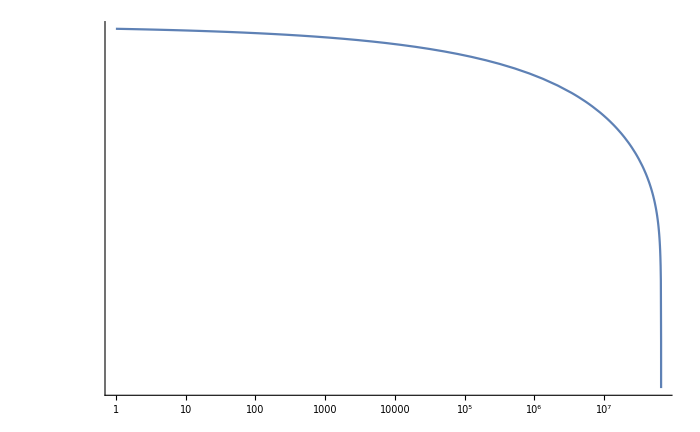

```mathematica
LogLogPlot[dimR,{M,1,10^10},PlotRange->{1000,All}]
```

```mathematica
FindMinimum[Re[StarRates[[1]]],M]
```

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

{0.255557,{M→6.53794×10^7}}

```mathematica
Reduce[0.95*(1+chi)<1]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

chi<0.0526316